```mathematica
(* IMPORT MODULES *)
ClearAll[m1,m2,m3]
loadDumpSaves=True;
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/hamiltonian.nb"];
NotebookEvaluate["modules/parameters.nb"];
NotebookEvaluate["modules/golden_search.nb"];
If[loadDumpSaves,NotebookEvaluate["modules/load_dump_saves.nb"]];
SetDirectory[NotebookDirectory[]];
```

```mathematica
(* For loop for calculating temperature curves *)
temps=Table[t,{t,0,1,0.1}];
dict=<|uq->"u",sq->"s",cq->"c",bq->"b"|>;
save=True;(* Do you want to save the results? *)

tData[J_,P_,flavourSym_,γMax_,Λ_,S_,mass1_,mass2_,mass3_,excited_]:=tData[J,P,flavourSym,γMax,Λ,S,mass1,mass2,mass3,excited]=Module[
{tempData},
tempData={};
For[iter=1,iter≤Length[temps],iter++,
temp=temps[[iter]];
m1=mass1;(* mass of quark 1 *)
m2=mass2;(* mass of quark 2 *)
m3=mass3;(* mass of quark 3 *)
temperature=temp;

(* all different masses = 0, two equal masses = 1, all equal masses = 2 *)
case=If[m1==m2,1,0];
case=If[m1==m2==m3,2,case];
states=allStates[J,P,Λ,S,γMax];
sM=stateMatrix[J,P,Λ,S,γMax];

(* Calculate generalised transformation matrices *)
{t1time,t1}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,1]];
(*Print["Time taken to compute t1: ", ToString[t1time]];*)
{t2time,t2}=AbsoluteTiming[tMatrix[J,P,Λ,S,γMax,m1,m2,m3,2]];
(*Print["Time taken to compute t2: ", ToString[t2time]];*)

(* Obtain projector matrix *)
proj=projector[states,flavourSym,case];

(* Required matrices for hamiltonian *)
vCoulomb=polynomialOperatorRho[sM,-1];(* 1/ρ matrix dimensionless *)
vLinear=polynomialOperatorRho[sM,1];(* ρ matrix dimensionless *)
qhoSpect=qhoSpectrum[sM];
kineticRho=polynomialOperatorRho[sM,2];
kineticLam=polynomialOperatorLambda[sM,2];
ham[ω_]:=Hb[ω,temperature,m1,m2,m3,proj];

(* Find minimum and errors*)
{minTime,{a,b,data}}=AbsoluteTiming[goldenSearch[ham,excited+1,0.001,0.9,0.0005]];
(*Print["Time taken to find minimum: ", ToString[minTime]];*)
wMin=(a+b)/2;
hamiltonian=ham[wMin];
eigvalMin=Eigenvalues[hamiltonian][[-excited-1]];
AppendTo[tempData,{temp,eigvalMin}];
Print[iter,". t = ", temp,", ω = ",wMin, ", E = ",eigvalMin];
(*Print["{ω_min, E_min}: ",{Around[wMin,a-wMin],eigvalMin}];
Print["Number of basis functions (matrix size): ", Length[hamiltonian]];*)

(* Dump Saves *)
If[loadDumpSaves,
DumpSave["modules/dumpSave/summationVariables.mx",summationVariables];
DumpSave["modules/dumpSave/talmi.mx",talmi];
DumpSave["modules/dumpSave/nineJ.mx",nineJ];
DumpSave["modules/dumpSave/rel.mx",rel];
DumpSave["modules/dumpSave/Rcoeff.mx",Rcoeff];
DumpSave["modules/dumpSave/Lcoeff.mx",Lcoeff];]
](* End of For loop *);
Print[tempData];
tempData
]

temperatureData[J_,P_,flavourSym_,γMax_,Λ_,S_,mass1_,mass2_,mass3_,excited_]:=Module[{tempData},
tempData=tData[J,P,flavourSym,γMax,Λ,S,mass1,mass2,mass3,excited];
If[loadDumpSaves&&save&&NumberQ[tempData[[1,2]]],
DumpSave["modules/dumpSave/temperature_data.mx",tData],
Print["Data not saved"]
];
tempData
]
```

## Comparing negative and positive parity states as function of T/T_c

1. t = 0., ω = 0.424347, E = 2.86338

2. t = 0.1, ω = 0.424347, E = 2.85745

3. t = 0.2, ω = 0.424347, E = 2.83942

4. t = 0.3, ω = 0.424347, E = 2.80859

5. t = 0.4, ω = 0.405402, E = 2.76358

6. t = 0.5, ω = 0.405402, E = 2.70188

7. t = 0.6, ω = 0.374749, E = 2.61965

8. t = 0.7, ω = 0.355804, E = 2.5095

9. t = 0.8, ω = 0.325151, E = 2.35673

10. t = 0.9, ω = 0.275553, E = 2.12062

11. t = 1., ω = 0.034799, E = 1.19774

{{0.,2.86338},{0.1,2.85745},{0.2,2.83942},{0.3,2.80859},{0.4,2.76358},{0.5,2.70188},{0.6,2.61965},{0.7,2.5095},{0.8,2.35673},{0.9,2.12062},{1.,1.19774}}

1. t = 0., ω = 0.424347, E = 2.88613

2. t = 0.1, ω = 0.424347, E = 2.88016

3. t = 0.2, ω = 0.424347, E = 2.86199

4. t = 0.3, ω = 0.405402, E = 2.83087

5. t = 0.4, ω = 0.405402, E = 2.78535

6. t = 0.5, ω = 0.405402, E = 2.72305

7. t = 0.6, ω = 0.374749, E = 2.63979

8. t = 0.7, ω = 0.355804, E = 2.5283

9. t = 0.8, ω = 0.325151, E = 2.37342

10. t = 0.9, ω = 0.275553, E = 2.13353

11. t = 1., ω = 0.034799, E = 1.19644

{{0.,2.88613},{0.1,2.88016},{0.2,2.86199},{0.3,2.83087},{0.4,2.78535},{0.5,2.72305},{0.6,2.63979},{0.7,2.5283},{0.8,2.37342},{0.9,2.13353},{1.,1.19644}}

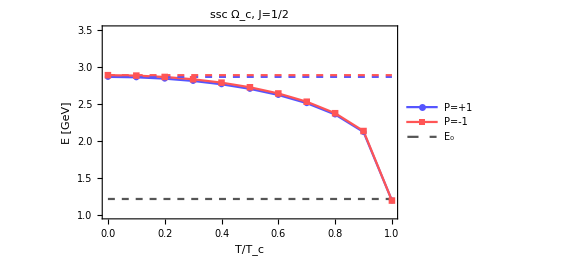

```mathematica
m1=uq;
m2=uq;
m3=cq;
fs=0;
gm=8;
excited=1;
pos=temperatureData[1/2,+1,fs,gm,0,1/2,m1,m2,m3,excited];
neg=temperatureData[1/2,-1,fs,gm,1,1/2,m1,m2,m3,excited];
imgSize=420;
imagePadding={{55,10},{50,10}};

SetOptions[ListPlot,
Frame->True,
Joined->True,
Axes->True,
ImagePadding->imagePadding,
FrameLabel->{"T/T_c","E [GeV]"},
PlotMarkers->{Automatic,Automatic,False,False,False},
ImageSize->imgSize,
LabelStyle->{FontFamily->"Arial",FontSize->14}];

plotLabels={pos[[-1,2]],neg[[-1,2]],m1+m2+m3-1/2(3Cqqq)};
plotPositions={{1.0005,pos[[-1,2]]},{1.0005,neg[[-1,2]]},{1.0005,m1+m2+m3-1/2(3Cqqq)}};
E0=m1+m2+m3-1/2(3Cqqq);
dashedLine=Table[{t,E0},{t,0,1,0.1}];
dashedPos=Table[{t,pos[[1,2]]},{t,0,1,0.1}];
dashedNeg=Table[{t,neg[[1,2]]},{t,0,1,0.1}];

main=ListPlot[{pos,neg,dashedLine,dashedPos,dashedNeg},
PlotLabel->"ssc Ω_c, J=1/2",
PlotStyle->{Lighter[Blue],Lighter[Red],{Lighter[Black],Dashed},{Lighter[Blue],Dashed,Thin},{Lighter[Red],Dashed,Thin}},
PlotLegends->Placed[{"P=+1","P=-1","E_0"},{After,Top}],
PlotRange->{Automatic,{1,3.5}}
]
```

```mathematica
Export["plots/ch8_ssc_jhalf_pVSn.pdf",main,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch8_ssc_jhalf_pVSn.pdf

## Single baryon excited states as function of T/T_c

1. t = 0., ω = 0.68412, E = 2.28186

2. t = 0.1, ω = 0.682646, E = 2.27769

3. t = 0.2, ω = 0.677625, E = 2.26505

4. t = 0.3, ω = 0.66925, E = 2.2434

5. t = 0.4, ω = 0.657015, E = 2.21179

6. t = 0.5, ω = 0.640012, E = 2.16858

7. t = 0.6, ω = 0.617017, E = 2.11103

8. t = 0.7, ω = 0.585647, E = 2.03423

9. t = 0.8, ω = 0.540879, E = 1.92815

10. t = 0.9, ω = 0.468192, E = 1.7655

11. t = 1., ω = 0.052777, E = 1.17039

{{0.,2.28186},{0.1,2.27769},{0.2,2.26505},{0.3,2.2434},{0.4,2.21179},{0.5,2.16858},{0.6,2.11103},{0.7,2.03423},{0.8,1.92815},{0.9,1.7655},{1.,1.17039}}

1. t = 0., ω = 0.406518, E = 3.09916

2. t = 0.1, ω = 0.405451, E = 3.09245

3. t = 0.2, ω = 0.402, E = 3.07206

4. t = 0.3, ω = 0.396009, E = 3.03713

5. t = 0.4, ω = 0.387381, E = 2.98604

6. t = 0.5, ω = 0.375303, E = 2.91609

7. t = 0.6, ω = 0.359054, E = 2.82268

8. t = 0.7, ω = 0.336874, E = 2.69759

9. t = 0.8, ω = 0.305504, E = 2.52386

10. t = 0.9, ω = 0.254745, E = 2.25491

11. t = 1., ω = 0.00703933, E = 1.19298

{{0.,3.09916},{0.1,3.09245},{0.2,3.07206},{0.3,3.03713},{0.4,2.98604},{0.5,2.91609},{0.6,2.82268},{0.7,2.69759},{0.8,2.52386},{0.9,2.25491},{1.,1.19298}}

1. t = 0., ω = 0.443065, E = 3.14454

2. t = 0.1, ω = 0.441747, E = 3.13766

3. t = 0.2, ω = 0.437733, E = 3.11675

4. t = 0.3, ω = 0.43083, E = 3.08093

5. t = 0.4, ω = 0.420981, E = 3.02857

6. t = 0.5, ω = 0.407177, E = 2.95686

7. t = 0.6, ω = 0.388699, E = 2.86114

8. t = 0.7, ω = 0.363727, E = 2.73298

9. t = 0.8, ω = 0.328498, E = 2.55504

10. t = 0.9, ω = 0.272563, E = 2.27979

11. t = 1., ω = 0.00546939, E = 1.19542

{{0.,3.14454},{0.1,3.13766},{0.2,3.11675},{0.3,3.08093},{0.4,3.02857},{0.5,2.95686},{0.6,2.86114},{0.7,2.73298},{0.8,2.55504},{0.9,2.27979},{1.,1.19542}}

1. t = 0., ω = 0.315353, E = 3.34728

2. t = 0.1, ω = 0.314287, E = 3.33985

3. t = 0.2, ω = 0.311495, E = 3.31729

4. t = 0.3, ω = 0.30657, E = 3.27862

5. t = 0.4, ω = 0.299009, E = 3.22207

6. t = 0.5, ω = 0.288908, E = 3.14462

7. t = 0.6, ω = 0.275355, E = 3.04115

8. t = 0.7, ω = 0.25713, E = 2.90247

9. t = 0.8, ω = 0.231247, E = 2.70962

10. t = 0.9, ω = 0.190182, E = 2.41029

11. t = 1., ω = 0.00424737, E = 1.19717

{{0.,3.34728},{0.1,3.33985},{0.2,3.31729},{0.3,3.27862},{0.4,3.22207},{0.5,3.14462},{0.6,3.04115},{0.7,2.90247},{0.8,2.70962},{0.9,2.41029},{1.,1.19717}}

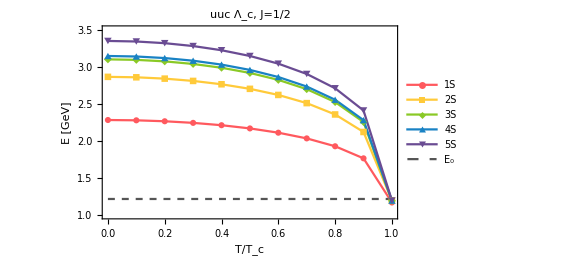

```mathematica
m1=uq;
m2=uq;
m3=cq;
fs=0;
gm=8;
pos1=temperatureData[1/2,+1,fs,gm,0,1/2,m1,m2,m3,0];
pos2=temperatureData[1/2,+1,fs,gm,0,1/2,m1,m2,m3,1];
pos3=temperatureData[1/2,+1,fs,gm,0,1/2,m1,m2,m3,2];
pos4=temperatureData[1/2,+1,fs,gm,0,1/2,m1,m2,m3,3];
pos5=temperatureData[1/2,+1,fs,gm,0,1/2,m1,m2,m3,4];
imgSize=420;
imagePadding={{50,10},{45,10}};

rgb[c1_,c2_,c3_]:=RGBColor[c1/255,c2/255,c3/255];

cScheme1={{rgb[234,172,139]},{rgb[229,107,111]},{rgb[181,101,118]},{rgb[109,89,122]},{rgb[53,80,112]},{Lighter[Black],Dashed,Thin}};
cScheme2={{rgb[246,170,28]},{rgb[188,57,8]},{rgb[148,27,12]},{rgb[98,23,8]},{rgb[34,9,1]},{Lighter[Black],Dashed,Thin}};
cScheme3={{rgb[255,89,94]},{rgb[255,202,58]},{rgb[138,201,38]},{rgb[25,130,196]},{rgb[106,76,147]},{Lighter[Black],Dashed,Thin}};

SetOptions[ListPlot,
Frame->True,
Joined->True,
Axes->True,
FrameLabel->{"T/T_c","E [GeV]"},
PlotMarkers->{Automatic,Automatic,Automatic,Automatic,Automatic,False},
ImagePadding->imagePadding,
ImageSize->imgSize,
PlotStyle->cScheme3,
LabelStyle->{FontFamily->"Arial",FontSize->14}];

E0=m1+m2+m3-1/2(3Cqqq);
dashedLine=Table[{t,E0},{t,0,1,0.1}];
dashedPos=Table[{t,pos[[1,2]]},{t,0,1,0.1}];
dashedNeg=Table[{t,neg[[1,2]]},{t,0,1,0.1}];

main=ListPlot[{pos1,pos2,pos3,pos4,pos5,dashedLine},
PlotLabel->"uuc Λ_c, J=1/2",
PlotLegends->Placed[{"1S","2S","3S","4S","5S","E_0"},{After,Top}],
PlotRange->{Automatic,{1,3.5}}
]
```

```mathematica
Export["plots/ch8_uuc_ladder.pdf",main,"AllowRasterization"->True,ImageSize->360,ImageResolution->600]
```

plots/ch8_uuc_ladder.pdf

## Expectation Values

```mathematica
hamiltonian=1
eigenvector=2
operatorMatrix=3
expectationValue=eigenvector.operator.eigenvector
```

1

2

3

2.3.2

```mathematica
?Hb
```